```mathematica
Import[FileNameJoin[{NotebookDirectory[],"nonR_master.wl"}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.051}

{0.9}

We consider the following parameters:

m = 1

n = 0

χ = 0.9

S = -1.

branch = 2

Log of precision cutoff = 10^-20

-------------------------------------

Picked S=-1 νnonrel

1/1

0.05

-1

8

Simplex code...

0.04993703125+1.×10^-9 ⅈ

Count: 2

Count: 3

Count: 4

Count: 5

Count: 6

Count: 7

Count: 8

Count: 9

Count: 10

Count: 11

Count: 12

Count: 13

Count: 14

Count: 15

Count: 16

Count: 17

Count: 18

Count: 19

Count: 20

Count: 21

Count: 22

Count: 23

Count: 24

Count: 25

Count: 26

Count: 27

Count: 28

Count: 29

Count: 30

Count: 31

Count: 32

Count: 33

Count: 34

Count: 35

Count: 36

Count: 37

Count: 38

Count: 39

Count: 40

Count: 41

Count: 42

Count: 43

Count: 44

Count: 45

Count: 46

Count: 47

Count: 48

Count: 49

Count: 50

Count: 51

Count: 52

Count: 53

Count: 54

Count: 55

Count: 56

Count: 57

Count: 58

Count: 59

Count: 60

Count: 61

Count: 62

Count: 63

Count: 64

Count: 65

Count: 66

Count: 67

Count: 68

Count: 69

Count: 70

Count: 71

Count: 72

Count: 73

Count: 74

Count: 75

Count: 76

Count: 77

Count: 78

Count: 79

Count: 80

Count: 81

Count: 82

Count: 83

Count: 84

Count: 85

Count: 86

Count: 87

Count: 88

Count: 89

Count: 90

Count: 91

Count: 92

Count: 93

Count: 94

Count: 95

Count: 96

Count: 97

Count: 98

Count: 99

Count: 100

Count: 101

Count: 102

Count: 103

Count: 104

Count: 105

Count: 106

Count: 107

Count: 108

Count: 109

Count: 110

Count: 111

Count: 112

Count: 113

Count: 114

Count: 115

Count: 116

Count: 117

Count: 118

Count: 119

Count: 120

Count: 121

Count: 122

Count: 123

Count: 124

Count: 125

Count: 126

Count: 127

Count: 128

Count: 129

Count: 130

Count: 131

Count: 132

Count: 133

Count: 134

Count: 135

Count: 136

Count: 137

Count: 138

Count: 139

Count: 140

Count: 141

Count: 142

Count: 143

Count: 144

Count: 145

Count: 146

Count: 147

Count: 148

Count: 149

Count: 150

Count: 151

Count: 152

Count: 153

Count: 154

Count: 155

Count: 156

Count: 157

Count: 158

Count: 159

Count: 160

Count: 161

Count: 162

Count: 163

Count: 164

Count: 165

Count: 166

Count: 167

Count: 168

Count: 169

Count: 170

Count: 171

Count: 172

0.0499370747889158798320323+9.241770256791293×10^-10 ⅈ

---------------------------------------------

172

7.61300384915095662332071×10^-30

Solving angular equation...

Done

2/1

0.051

-1

9

Simplex code...

0.05093311487859375+9.24177025679×10^-10 ⅈ

Count: 2

Count: 3

Count: 4

Count: 5

Count: 6

Count: 7

Count: 8

Count: 9

Count: 10

Count: 11

$Aborted

```mathematica
ωminout
```

ωminout

```mathematica
(*Looks like this code also runs into the problem of higher overtones secretely existing near the horizon*)
```

```mathematica
res = Import[FileNameJoin[{NotebookDirectory[], "surrogate/m1n0_a900000_Sm1_prec_p_HPee.mx"}]];
```

InterpolatingFunction[…]

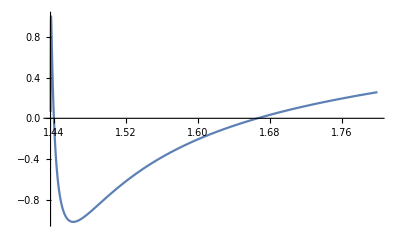

```mathematica
res[[-2]][[1]][[1]][[2]]
Plot[%[r]//Re, {r,1.436, 1.8}, PlotRange->All]
```

```mathematica
QNMcode`funcmin[res[[-3]][[1]],(QNMcode`rν+I*QNMcode`iν)/.res[[-4]][[1]],0.05,2]
```

QNMcode`funcmin[0.0499370747889158798320323+9.241770256791293×10^-10 ⅈ,-0.0523309578563064339645293-3.68024201684809784924316×10^-10 ⅈ,0.05,2]

-0.0523309578563064339645293-3.68024201684809784924316×10^-10 ⅈ

InterpolatingFunction[…]

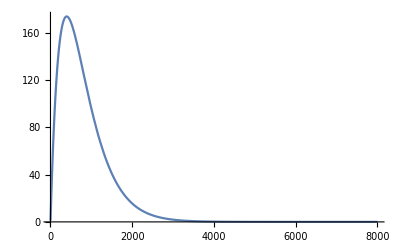

```mathematica
res[[-2]][[1]][[1]][[2]]
Plot[%[r]//Abs, {r,1.52, 8000}, PlotRange->All]
```

```mathematica
solR
```

solR